## General Stuff

### SDPB Function

```mathematica
sdpboutputjdg[message_]:=Which[StringContainsQ[message,"found primal-dual optimal solution"],"found primal-dual optimal solution",StringContainsQ[message,"found primal feasible solution"],"found primal feasible solution",StringContainsQ[message,"found dual feasible solution"],"found dual feasible solution",StringContainsQ[message,"primal feasible jump detected"],"primal feasible jump detected",StringContainsQ[message,"dual feasible jump detected"],"dual feasible jump detected",StringContainsQ[message,"maxIterations exceeded"],"maxIterations exceeded",StringContainsQ[message,"maxRuntime exceeded"],"maxRuntime exceeded",StringContainsQ[message,"maxComplementarity exceeded"],"maxComplementarity exceeded"];
```

```mathematica
Readfunctionalraw[file_,num_]:=Module[{tem,vec},
tem=Table[Import[file,{"Lines",i}]//StringReplace[#,"e"->"*10^"]&//ToExpression,{i,2,num}];
tem
]
```

```mathematica
restoreCoefficients[yVector_,norm_]:=Module[
	{α,j=maxIndexBy[norm,Abs],length=Length[norm],shortNorm},
	shortNorm=Delete[norm,j];
α=Array[#/.{i_:>yVector[[i]]/;i<j,i_:>yVector[[i-1]]/;i>j,i_:>(1-yVector.shortNorm)/norm[[j]]/;i==j}&,length];
	Return[α];
];
```

```mathematica
Readfunctional[input_,norm_]:=Module[{num,rawvec,yvec,filename},
filename=StringJoin[{input,"_out/y.txt"}];
num=Length[norm];
rawvec=Readfunctionalraw[filename,num];
yvec=restoreCoefficients[rawvec,norm];
yvec
]
```

```mathematica
runsdpbfeasbility[file_,input_]:=If[os=="mac",runsdpbmacfeasbility[file,input],runsdpbwin10feasibility[file,input]];
```

```mathematica
runsdpbmacfeasbility[file_,input_]:=Module[{message,jdg},
RunProcess[{"docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"pvm2sdp","1024",StringJoin[{"/data/",file}],StringJoin[{"/data/",input}]},"StandardOutput",ProcessEnvironment-><|"PATH"->"/usr/local/bin:"<>Environment["PATH"]|>];
message=RunProcess[{"docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"sdpb","--precision=1024","--maxIterations=1000","--primalErrorThreshold=1e-40","--dualErrorThreshold=1e-40","--dualityGapThreshold=1e-60",StringJoin[{"--procsPerNode=",nodenum//ToString}],"--detectPrimalFeasibleJump","--detectDualFeasibleJump","-s",StringJoin[{"/data/",input}]},"StandardOutput",ProcessEnvironment-><|"PATH"->"/usr/local/bin:"<>Environment["PATH"]|>]//ToString;
sdpboutputjdg[message]
]
```

```mathematica
runsdpbwin10feasibility[file_,input_]:=Module[{message,jdg},
RunProcess[{"powershell","docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"pvm2sdp","1024",StringJoin[{"/data/",file}],StringJoin[{"/data/",input}]},"StandardOutput"];
message=RunProcess[{"powershell","docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"sdpb","--precision=1024","--maxIterations=1000","--primalErrorThreshold=1e-40","--dualErrorThreshold=1e-40","--dualityGapThreshold=1e-60"，StringJoin[{"--procsPerNode=",nodenum//ToString}],"--detectPrimalFeasibleJump","--detectDualFeasibleJump","-s",StringJoin[{"/data/",input}]},"StandardOutput"];
sdpboutputjdg[message]
]
```

```mathematica
runsdpbmacobj[file_,input_]:=Module[{message},
RunProcess[{"docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"pvm2sdp","1024",StringJoin[{"/data/",file}],StringJoin[{"/data/",input}]},"StandardOutput",ProcessEnvironment-><|"PATH"->"/usr/local/bin:"<>Environment["PATH"]|>];
message=RunProcess[{"docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"sdpb","--precision=1024",StringJoin[{"--procsPerNode=",nodenum//ToString}],"-s",StringJoin[{"/data/",input}]},"StandardOutput",ProcessEnvironment-><|"PATH"->"/usr/local/bin:"<>Environment["PATH"]|>]//ToString;
sdpboutputjdg[message]
]
```

```mathematica
runsdpbwin10obj[file_,input_]:=Module[{message},
RunProcess[{"powershell","docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"pvm2sdp","1024",StringJoin[{"/data/",file}],StringJoin[{"/data/",input}]},"StandardOutput"];
message=RunProcess[{"powershell","docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"sdpb","--precision=1024",StringJoin[{"--procsPerNode=",nodenum//ToString}],"-s",StringJoin[{"/data/",input}]},"StandardOutput"];
sdpboutputjdg[message]
]
```

```mathematica
runsdpbobj[file_,input_]:=If[os=="mac",runsdpbmacobj[file,input],runsdpbwin10obj[file,input]];
```

```mathematica
getspectrummacminz0[cc_,xmlfile_,input_]:=Module[{rawdata,zerotable,Prec,tb1,tb2,tb3,tb4},
Prec=10;
RunProcess[{"docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"spectrum",StringJoin["--input=data/",xmlfile],StringJoin["--solution=data/",input,"_out"],StringJoin["--threshold=1e-",ToString[Prec]],"--format=PVM","--output=data/new.json","--precision=1024"},"StandardOutput",ProcessEnvironment-><|"PATH"->"/usr/local/bin:"<>Environment["PATH"]|>];
rawdata=Import["new.json"];
tb1="zeros"/.rawdata//{"zero","lambda"}/.#&;
tb2=Table[0,{i,1,Length[tb1]}];
Do[tb2[[i]]=(tb1[[i]]//#/.{a_,{b_}}:>{ToExpression[StringReplace[a,"e"->"*10^"]]+i-1,ToExpression[StringReplace[b,"e"->"*10^"]],i-1}&),{i,1,Length[tb1]}];
tb3=tb2//DeleteCases[#,{"zero","lambda"}]&//Flatten[#,1]&;
tb4=Table[{tb3[[i,1]],tb3[[i,3]],2 tb3[[i,2]]^2/DampedRational[E^(-π/6+cc π/6),{},E^(-2π),tb3[[i,1]]]},{i,1,Length[tb3]}];
DeleteFile["new.json"];
tb4
]
```

```mathematica
getspectrumwin10minz0[cc_,xmlfile_,input_]:=Module[{rawdata,zerotable,Prec,tb1,tb2,tb3,tb4},
Prec=10;
RunProcess[{"powershell","docker","run","-v",StringJoin[{StringReplace[dir,"\\"->"/"],":/data"}],StringJoin["wlandry/sdpb:",SDPBversion],"mpirun","--allow-run-as-root","--oversubscribe","-np",nodenum//ToString,"spectrum",StringJoin["--input=data/",xmlfile],StringJoin["--solution=data/",input,"_out"],StringJoin["--threshold=1e-",ToString[Prec]],"--format=PVM","--output=data/new.json","--precision=1024"},"StandardOutput"];
rawdata=Import["new.json"];
tb1="zeros"/.rawdata//{"zero","lambda"}/.#&;
tb2=Table[0,{i,1,Length[tb1]}];
Do[tb2[[i]]=(tb1[[i]]//#/.{a_,{b_}}:>{ToExpression[StringReplace[a,"e"->"*10^"]]+i-1,ToExpression[StringReplace[b,"e"->"*10^"]],i-1}&),{i,1,Length[tb1]}];
tb3=tb2//DeleteCases[#,{"zero","lambda"}]&//Flatten[#,1]&;
tb4=Table[{tb3[[i,1]],tb3[[i,3]],2 tb3[[i,2]]^2/DampedRational[2,{},E^(-2π),tb3[[i,1]]]},{i,1,Length[tb3]}];
DeleteFile["new.json"];
tb4
]
```

```mathematica
getspectrumminz0[cc_,xmlfile_,input_]:=If[os=="mac",getspectrummacminz0[cc,xmlfile,input],getspectrumwin10minz0[cc,xmlfile,input]]
```

### Linear reduce

```mathematica
Nprec=200;
```

```mathematica
Fmatfib={{ξ^-1,ξ^(-1/2)},{ξ^(-1/2),-ξ^-1}}//#/.ξ->(1+Sqrt[5])/2&;
k0=SetPrecision[16 E^-π,Nprec];
```

```mathematica
LRFmatchiral[Fmat_,Λmax_]:=Module[{dimF,zerovec,evenvec,oddvec,evenTB,oddTB},
dimF=Length[Fmat];
zerovec=Table[0,{i,1,dimF}];
evenvec=IdentityMatrix[dimF]-Rationalize[Fmat]//RowReduce//FullSimplify//DeleteCases[#,zerovec]&;
oddvec=IdentityMatrix[dimF]+Rationalize[Fmat]//RowReduce//FullSimplify//DeleteCases[#,zerovec]&;
oddTB=Table[zderivwithDelta[k]SetPrecision[oddvec,Nprec],{k,1,Λmax,2}]//Flatten[#,1]&;
evenTB=Table[zderivwithDelta[k]SetPrecision[evenvec,Nprec],{k,0,Λmax,2}]//Flatten[#,1]&;
Transpose[Flatten[{oddTB,evenTB},1]]
]
```

Each vector of the final output is:
∑_O_1 (λ_ϕϕO_1)^2(F⃗)_O_1+∑_O_2 (λ_ϕϕO_2)^2(F⃗)_O_2+...+∑_O_n (λ_ϕϕO_n)^2(F⃗)_O_n=OverVector[0], where i=1,2,..n labels operators in different twisted Hilbert space

### Compute Virasoro blocks

The following code is almost exactly copied from the code at arXiv:1703.09727

```mathematica
Nprec=200;
```

```mathematica
ClearAll[qCoeffient,Nprecision];

Nprecision=Nprec;(*Max[500,IntegerPart[c+300]];*)(*300;*)(*Set precision*)
(*$MinPrecision=Nprecision;*)

(*qCoeffient returns the q-expansion coefficients. The inputs of qCoefficient[] are the the central charge cCentralCharge, light-operator dimension hLight, the heavy-operator dimension hHeavy, the intermediate operator dimension hIntermediate, and the highest power of the coefficients NN wanted.*)

qCoeffient[cCentralCharge_,hLight_,hHeavy_,hIntermediate_,NN_]:=qCoeffient[cCentralCharge,hLight,hHeavy,hIntermediate,NN]=Block[{c,hL,hH,b,h,countmn,lengthmn,startmn,Cij,CHij,λLsquare,λHsquare,λpq,Ppq,Rmn,RmnDenominator,RmnList,hmnList,mnhalfList,temp,NNhalf=Floor[NN/2],qCoefList=Table[0,Floor[NN/2]+1]},

(*NNhalf is number of terms in the list of the coefficients qCoefList that need to be calculated, since only even powers of q are non-zero.*)

(*Convert the arguments to high precision decimals. Do nothing for symbolic calculation.*)
hL=If[NumberQ[hLight],N[Rationalize[hLight],Nprecision],hLight];
hH=If[NumberQ[hHeavy],N[Rationalize[hHeavy],Nprecision],hHeavy];
c=If[NumberQ[cCentralCharge],N[Rationalize[cCentralCharge],Nprecision],cCentralCharge];
b=If[NumberQ[c],N[Rationalize[(√(c-13+√(c^2-26 c+25)))/(2 √3)],Nprecision],b];(*For symbolic calculation, present the result in terms of b.*)
h=If[NumberQ[hIntermediate],N[Rationalize[hIntermediate],Nprecision],hIntermediate];

λLsquare=1/4(b+1/b)^2-hL;(*Subscript[λ, L]^2*)
λHsquare=1/4(b+1/b)^2-hH;(*Subscript[λ, H]^2*)
λpq[p_,q_]:=1/2(p/b+q b);(*Subscript[λ, p,q]*)

Ppq[p_,q_]:=(λpq[p,q]^2-4λLsquare)(λpq[p,q]^2-4λHsquare ) λpq[p,q]^4;(*Ppq[p,q] gives the contribution to the numerator of Subscript[R, m,n] from Subscript[λ, p,q] and Subscript[λ, -p,-q]*)

RmnDenominator[m_,n_]:=Product[Piecewise[{{1,k==0&&l==0},{1,k==m&&l==n}},(k/b+l b)/2],{k,-m+1,m},{l,-n+1,n}];
(*RmnDenominator[m,n] give the denominator of Subscript[R, m,n], but only to be used for calculation of the first several terms of Subscript[R, m,n].*)

(*Subscript[R, m,n] is filled recursively from higher order terms, but we need to set the boundary values for this recursive calculation.*)
Rmn=Table[0,NN,NN];
Rmn[[1,2]]=2 Ppq[0,1]/RmnDenominator[1,2];
Rmn[[2,1]]=2 Ppq[1,0]/RmnDenominator[2,1];
Rmn[[2,2]]=2(Ppq[1,-1]Ppq[1,1])/RmnDenominator[2,2];
(*Obtain Subscript[R, m,1] and Subscript[R, m,2] from Subscript[R, m-2,1] and Subscript[R, m-2,2] respectively*)
Do[Rmn[[m,1]]=Rmn[[m-2,1]]/λpq[m-2,1] Ppq[m-1,0]λpq[m,1]Product[2/(k/b+nn b),{nn,0,1},{k,{-m+1,-m+2,m-1,m}}],{m,4,NN,2}];
Do[Rmn[[m,2]]=Rmn[[m-2,2]]/λpq[m-2,2] Ppq[m-1,-1]Ppq[m-1,1]λpq[m,2]Product[2/(k/b+nn b),{nn,-1,2},{k,{-m+1,-m+2,m-1,m}}],{m,3,NN}];
(*Obtain Subscript[R, m,n] from Subscript[R, m,n-2], only calculate terms with even mn*)
Do[Rmn[[m,n]]=If[OddQ[m n],0,Rmn[[m,n-2]]/λpq[m,n-2] λpq[m,n]Product[Ppq[p,n-1],{p,-m+1,m-1,2}]Product[2/(k/b+nn b),{nn,{-n+1,-n+2,n-1,n}},{k,-m+1,m}]],{m,1,NN},{n,3,NN/m}];

(*In the following calculation, Subscript[R, m,n] and Subscript[h, m,n] are stored into one-dimensional tables, and we only need to consider cases that mn is even*)

startmn=Table[0,Floor[NN/2]+1];
lengthmn=0;
Do[startmn[[i]]=lengthmn;lengthmn+=Length[Divisors[2i]],{i,1,NNhalf+1}];
lengthmn-=Length[Divisors[2(NNhalf+1)]];
(*lengthmn counts the length of these one-dimension tables, which is the sum of the number of divisors of even integers up to NN*)
(*Elements from startmn[[i]]+1 to startmn[[i+1]] of these one-dimensioanl tables to be defiend below  correspond to the Subscript[R, m,n] and Subscript[h, m,n] who have mn/2=i.*)  

RmnList=Table[0,lengthmn];
hmnList=Table[0,lengthmn];
mnhalfList=Table[0,lengthmn];

(*RmnList and hmnList are used to stores Subscript[h, m,n] and Subscript[R, m,n] into a one-dimensional tables. Those Subscript[h, m,n] s with the same product mn will be stored in hmnList from startmn[[mn/2]]+1 to startmn[[mn/2+1]], and similar for RmnList.*)
(*mnhalfList stores the number mn/2 that corresponds to the each element in these one-dimensional tables, for example mnhalfList[[1]]=1 ((1*2)/2==1), mnhalfList[[2]]=1 ((2*1)/2==1), mnhalfList[[3]]=2 ((1*4)/2==2), and so on*)

(*Below is how we construct these one-dimensional tables.*)
countmn=Table[0,NNhalf];
Do[If[EvenQ[m n],(temp=m n/2;countmn[[temp]]++;mnhalfList[[startmn[[temp]]+countmn[[temp]]]]=temp;RmnList[[startmn[[temp]]+countmn[[temp]]]]=Rmn[[m,n]];hmnList[[startmn[[temp]]+countmn[[temp]]]]=1/4(b+1/b)^2-λpq[m,n]^2),0],{m,1,NN},{n,1,NN/m}];
(*countmn[[temp]] records the number of divisors of 2temp that we encounters so far, so startmn[[temp]]+countmn[[temp]] is the position where the current element should be in these one-dimensional tables*)

HH=Table[Table[0,startmn[[i+1]]],{i,1,NNhalf}];(*HH[[i,j]] stores Subscript[H, m,n]^k in the diagonal way, as explained in the paper, where the fist index corresponds to the total power of Subscript[H, m,n]^k, which is i==(k+mn)/2 and the second index corresponds to (m,n). The length of HH[[i]] is startmn[[i+1]], which is the number of ways to write 2i as 2i==k+mn.*)

Do[HH[[i,j]]=1,{i,1,NNhalf},{j,startmn[[i]]+1,startmn[[i+1]]}];(*Subscript[H, m,n]^0=1*)

Cij=Table[RmnList[[j]]/(hmnList[[i]]+2mnhalfList[[i]]-hmnList[[j]]),{i,1,lengthmn},{j,1,startmn[[NNhalf-mnhalfList[[i]]+1]]}];(*Store the prefactors Subscript[C, ij]=Subscript[R, p,q]/(Subscript[h, m,n]+mn-Subscript[h, p,q]) into a two-dimensional table, where the first index corresponds to (m,n) and the second index corresponds to (p,q)*)

CHij=Table[RmnList[[i]]/(h-hmnList[[i]]),{i,1,lengthmn}];(*CHij is the list of prefactor to get the q-expansion coefficients in qCoefList, which are denoted as H^k in the paper*)

Do[Do[HH[[khalf+mnhalfList[[i]],i]]=Take[Cij[[i]],startmn[[khalf+1]]].HH[[khalf]],{i,1,startmn[[NNhalf-khalf+1]]}],{khalf,1,NNhalf}];
(*Calculate the Subscript[H, m,n]^k elements, this is the slow part of the code. The order that we conduct this calculation is that we calculate all the  Subscript[H, m,n]^k s with the same k, which can be obtained from HH[[k/2]], and then put them in the right places in HH[[]]. This process is explained in the Figure 19 of the paper.*)

qCoefList[[1]]=1;
Do[qCoefList[[i+1]]=Take[CHij,startmn[[i+1]]].HH[[i]],{i,1,NNhalf}];(*Construct the q-expansion coefficient H^k.*)
qCoefList]
```

```mathematica
qCoeffientmod2[cCentralCharge_,hLight_,hHeavy_,NN_]:=Module[{qcoeff,length,numerator,denominator,totaldenominatortb,poletb,qCoeffient2,qcoefftb,qcoeffMod,positb,polestb,testtb},
qcoeff=qCoeffient[cCentralCharge,hLight,hHeavy,h,NN]//Chop//#/.Complex[a1_,a2_]/(Complex[a3_,a4_]+h):>(a2 a4+a1 (a3+h))/(a4^2+(a3+h)^2)&;
length=Length[qcoeff];
qcoefftb=Table[Transpose[{Numerator[Apply[List,qcoeff[[i]]]],Denominator[Apply[List,qcoeff[[i]]]]}],{i,3,length}];
qcoefftb=Join[{{{1,1}},{{Numerator[qcoeff[[2]]],Denominator[qcoeff[[2]]]}}},qcoefftb];
totaldenominatortb={qcoefftb[[2,1,2]],qcoefftb[[3;;-1,All,2]]}//Flatten//Union;
qcoeffMod=Table[
Sum[qcoefftb[[i,j,1]]Apply[Times,DeleteCases[totaldenominatortb,qcoefftb[[i,j,2]]]],{j,1,Length[qcoefftb[[i]]]}],
{i,1,length}];(*Can be parallel!!*)
positb=Position[Exponent[totaldenominatortb,h],1]//Flatten;
polestb=totaldenominatortb[[positb]];
testtb=Table[PolynomialQ[qcoeffMod[[i]],h],{i,1,length}];
{Apply[Times,totaldenominatortb],polestb,qcoeffMod}(*,qcoeffMod*)
](*Fastest*)
```

```mathematica
qCoeffientmod2[3,3,3,6][[3,2]]//N
```

2. (23.3941+(-4.79167+h)^2) (4.29688+(-1.625+h)^2) (166.719+253. (-0.125+h)) (0.25+h) (0.477431+(0.208333+h)^2)

```mathematica
Computechiralblocktb[c_,hphi_,qN_,Fmat_,Λmax_]:=Module[{crational,hLrational,hHrational,qNrational,qCoeffientmod,Vblock,coeffpolytblist,funlist2,numerator,denominator,totaldenominator,poletbchiral2,poletbchiral,poletb,polytb,idtb,Veclist,prefactor},
{crational,hLrational,hHrational,qNrational}=Rationalize[{c,hphi,hphi,qN}];
{totaldenominator,poletbchiral2,qCoeffientmod}=qCoeffientmod2[crational,hLrational,hLrational,qN];
poletbchiral=Table[NSolve[poletbchiral2[[i]]==0,h][[1,1,-1]],{i,1,Length[poletbchiral2]}];
Veclist=LRFmatchiral[Fmat,Λmax];
Vblock=(16^(-(crational-1)/24) Exp[h π](q)^(h-(crational-1)/24)z^((crational-1)/24-hHrational-hLrational)(1-z)^((crational-1)/24-hHrational-hLrational)EllipticTheta[3,0,q]^((crational-1)/2-8(hHrational+hLrational))Table[q^i,{i,0,qNrational,2}].qCoeffientmod)/.q->Exp[-π EllipticK[1-z]/EllipticK[z]];
coeffpolytblist=Table[m!SeriesCoefficient[Vblock,{z,1/2,m}]//Expand//#/.ⅇ^a_:>ⅇ^Simplify[a]&//SetPrecision[#,Nprec]&,{m,0,Λmax,1}];


polytb=Table[i/.zderivwithDelta[a_]:>(coeffpolytblist[[a+1]]),{i,Veclist}];
{totaldenominator,polytb}

](*input for SDPB*)
```

## Fibonacci

### Bounding gap in k_w(z)...

```mathematica
hgapFeasibiltyFibonacci[c_,Fmat_,hϕ_,hg_,qN_,Λmax_] :=
Module[
{
unitOp,
norm,
obj,
polytb,
poletb,
hphi=SetPrecision[hϕ,Nprec],
cc=SetPrecision[c,Nprec],
file="hgapfes.xml",
input="hgapfes",
hgap=SetPrecision[hg,Nprec],
prefactor,
polstb,
spinlist,
gaplist,
temmessage,
totaldenominator,
functional
},
{totaldenominator,polytb}=Computechiralblocktb[c,hphi,qN,Fmat,Λmax];

polstb=Table[0,{i,1,Length[polytb]}];
polstb[[1]]=PositiveMatrixWithPrefactor[DampedRational[1,{},k0,x],{{polytb[[1]]/.h->x}}];
polstb[[2]]=PositiveMatrixWithPrefactor[DampedRational[1,{},k0,x],{{polytb[[2]]/.h->x+hgap}}];
unitOp=(1/totaldenominator polytb[[1]])/.h->0;
norm=unitOp;
obj=0*norm;
WriteBootstrapSDP[file,SDP[obj,norm,polstb]];
temmessage=runsdpbfeasbility[file,input];
functional=Readfunctional[input,norm]//{(#.polytb[[1]] k0^h)/totaldenominator,(#.polytb[[2]] k0^h)/totaldenominator}&;
DeleteFile[file];
DeleteFile[input];
DeleteDirectory[{StringJoin[{input,".ck"}],StringJoin[{input,"_out"}]},DeleteContents->True];

{temmessage,functional}

]
```

```mathematica
hgapFeasibiltyFibonacciwithoutblock[c_,Fmat_,hϕ_,hg_,qN_,Λmax_,blockinput_] :=
Module[
{
unitOp,
norm,
obj,
polytb,
poletb,
hphi=SetPrecision[hϕ,Nprec],
cc=SetPrecision[c,Nprec],
file="hgapfes.xml",
input="hgapfes",
hgap=SetPrecision[hg,Nprec],
prefactor,
polstb,
spinlist,
gaplist,
temmessage,
totaldenominator,
functional
},
{totaldenominator,polytb}=blockinput;

polstb=Table[0,{i,1,Length[polytb]}];
polstb[[1]]=PositiveMatrixWithPrefactor[DampedRational[1,{},k0,x],{{polytb[[1]]/.h->x}}];
polstb[[2]]=PositiveMatrixWithPrefactor[DampedRational[1,{},k0,x],{{polytb[[2]]/.h->x+hgap}}];
unitOp=(1/totaldenominator polytb[[1]])/.h->0;
norm=unitOp;
obj=0*norm;
WriteBootstrapSDP[file,SDP[obj,norm,polstb]];
temmessage=runsdpbfeasbility[file,input];
functional=Readfunctional[input,norm]//{(#.polytb[[1]] k0^h)/totaldenominator,(#.polytb[[2]] k0^h)/totaldenominator}&;
DeleteFile[file];
DeleteFile[input];
DeleteDirectory[{StringJoin[{input,".ck"}],StringJoin[{input,"_out"}]},DeleteContents->True];

{temmessage,functional}

]
```

```mathematica
binaryhgapFibkw[ini_,final_,Fmat_,c_,hp_,qN_,Λmax_,thesh_]:=Module[{ini1,final1,temmessage,finalfun,blockinput},
ini1=ini;
final1=final;
blockinput=Computechiralblocktb[c,hp,qN,Fmat,Λmax];
While[Abs[final1-ini1]>=thesh,temmessage=hgapFeasibiltyFibonacciwithoutblock[c,Fmat,hp,(ini1+final1)/2,qN,Λmax,blockinput][[1]]; If[temmessage=="found primal-dual optimal solution"||temmessage=="dual feasible jump detected",final1=(ini1+final1)/2,ini1=(ini1+final1)/2]];
finalfun=hgapFeasibiltyFibonacciwithoutblock[c,Fmat,hp,final1,qN,Λmax,blockinput];
{final1,finalfun[[1]],finalfun[[2]]}
]
```

### Run

```mathematica
dir=SetDirectory[NotebookDirectory[]];
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name<>".WXF"]//BinaryDeserialize;
```

```mathematica
<<"SDPB.m"
Nprec=200;
k0=SetPrecision[16 Exp[-π],Nprec];
os="win10";(*"mac" or "win10"*)
nodenum=20;
SDPBversion="2.5.1";
$MinPrecision=200;
```

```mathematica
Fmatfib={{ξ^-1,ξ^(-1/2)},{ξ^(-1/2),-ξ^-1}}//#/.ξ->(1+Sqrt[5])/2&;
```

#### (G_2)_1

```mathematica
data5=binaryhgapFibkw[7/5-1/5,7/5+1/5,Fmatfib,14/5,2/5,7,5,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
data7=binaryhgapFibkw[7/5-1/5,7/5+1/5,Fmatfib,14/5,2/5,10,7,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
data9=binaryhgapFibkw[7/5-1/5,7/5+1/5,Fmatfib,14/5,2/5,12,9,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
data11=binaryhgapFibkw[7/5-1/5,7/5+1/5,Fmatfib,14/5,2/5,14,11,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
data13=binaryhgapFibkw[7/5-1/5,7/5+1/5,Fmatfib,14/5,2/5,16,13,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
(*************7/10 Subscript[Λ, max]=15, gap goes up...Must be numerical issue. 1.Increase precision 2.Use linear programming***********)
```

```mathematica
{data5,data7,data9,data11}=binaryGet["hgapFib"];
```

#### (F_4)_1

```mathematica
hgapFeasibiltyFibonacci[26/5,Fmatfib,3/5,3/5+1+1/2,10,7][[1]]
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

dual feasible jump detected

```mathematica
F4data5=binaryhgapFibkw[3/5-1/5,3/5+1+1/2,Fmatfib,26/5,3/5,6,5,10^-5];
```

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
F4data7=binaryhgapFibkw[3/5-1/5,3/5+1+1/2,Fmatfib,26/5,3/5,10,7,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
F4data9=binaryhgapFibkw[3/5-1/5,3/5+1+1/2,Fmatfib,26/5,3/5,12,9,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
F4data11=binaryhgapFibkw[3/5-1/5,3/5+1+1/2,Fmatfib,26/5,3/5,14,11,10^-5];
```

SetPrecision::precsm: 要求的精度 5 小于 $MinPrecision. 使用 $MinPrecision.

General::stop: 在本次计算中，SetPrecision::precsm 的进一步输出将被抑制.

```mathematica
{F4data5,F4data7,F4data9,F4data11}=binaryGet["hgapFibF4"];
```

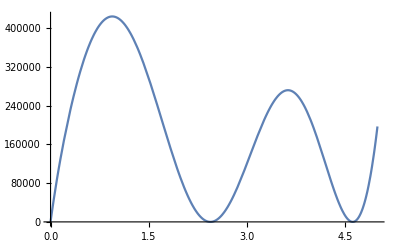

```mathematica
F4data11[[3,1]]//Plot[#,{h,0,5}]&
```